```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"];
Get["MaTeX`"];
ConfigureMaTeX["pdfLaTeX"->"/usr/local/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"];
SetOptions[Plot,FrameTicks->{{LinTicks,None},{LinTicks,None}}];
SetOptions[MaTeX,Magnification->1.5];
makeunit[label_,unit_]:=MaTeX[StringJoin[label,"\\ [\\textrm{",unit,"}]"]]
makeframelabel[xlabel_,xunit_,ylabel_,yunit_]:=FrameLabel->{makeunit[xlabel,xunit],makeunit[ylabel,yunit]}
Get["/Users/user1/Downloads/04/2022 05 26/WilsonInput.wl"];
```

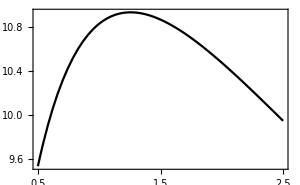

```mathematica
(* Assume constant impedance *)
(* Assume 1 dimension *)
(* Assume no beam i.e. unloaded *)
(* vzero unloaded constant impedance energy gain of whole structure *)
vzero[r_,L_,tau_,pzero_]:=(r*L*pzero)^(1/2)(2/tau)^(1/2)*(1-E^(-tau))
Plot[vzero[r,L,tau,pzero]/mega,{tau,0.5,2.5},FrameLabel->{MaTeX["\\tau"],MaTeX["V_0\\ [MV]"]}]
```

```mathematica
(* Set the attenuation parameter to the peak of this function *)
tau=tau/.Last[FindMaximum[vzero[r,L,tau,pzero],{tau,1.0}]]
```

1.25643

```mathematica
(* vzero*(rLpzero)^(-1/2) is 0.9 *)
vzero[r,L,tau,pzero]*(r*L*pzero)^(-1/2)
```

0.902512

```mathematica
(* alpha attenutation parameter per unit length *)
alpha=tau/L
```

2.09405 per meter

```mathematica
(* vgroup group velocity *)
vgroup=omega/(2*Q*alpha);
beta=vgroup/c
```

0.00684409

```mathematica
(* Magnitude of power out of the structure *)
E^(-tau)
```

0.284668

```mathematica
(* Power coming out of the structure *)
E^(-2tau)
```

0.0810359

```mathematica
lambdaBar=c/omega
```

0.00513048 m

```mathematica
lambda=c/(omega/(2*Pi))
```

0.0322357 m

```mathematica
((2*Pi*lambda*r)/(Q*beta))^(1/2)
```

791.64 √Ω

```mathematica
(* The accelerating electric field at the start of the structure *)
ezero[alpha_,r_,pzero_]:=(2*alpha*r*pzero)^(1/2)
```

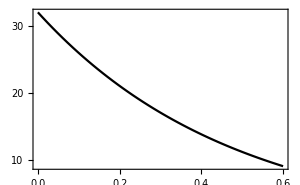

```mathematica
(* Unloaded constant impedance. The accelerating electric field as function of z *)
cze[alpha_,r_,pzero_,z_]:=ezero[alpha,r,pzero]*E^(-alpha*Quantity[z,"Meters"])
Plot[cze[alpha,r,pzero,z]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","E","MV/m"]],PlotRange->{{All,All},{0,All}}]
```

```mathematica
cze[alpha,r,pzero,0]
```

3.20195×10^7 √Ω √W/m

```mathematica
cze[alpha,r,pzero,QuantityMagnitude[L]]
```

9.11493×10^6 √Ω √W/m

```mathematica
(* 32 MV/m, high? *)
(* Note Root(Ohm * Watt) is Volts *)
(* The electric field at end of structure *)
eLUnloaded=ezero[alpha,r,pzero]*E^(-tau)
```

9.11493×10^6 √Ω √W/m

```mathematica
(* The power at end of structure *)
pLUnloaded=pzero*E^(-2*tau)
```

137761. W

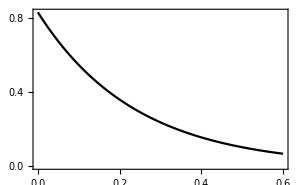

```mathematica
(* Unloaded constant impedance. The total stored energy per unit length in the propagating wave *)
w[alpha_,r_,pzero_,z_]:=(cze[alpha,r,pzero,z]^2*Q)/(omega*r)
Plot[w[alpha,r,pzero,z],{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","w","J/m"]]]
```

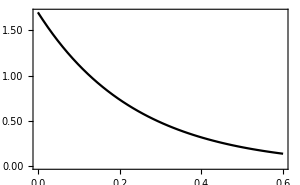

```mathematica
(* 5.10b Unloaded constant impedance. The power flow along the structure *)
p[pzero_,alpha_,z_]:=pzero*E^(-2*alpha*Quantity[z,"Meters"])
Plot[p[pzero,alpha,z]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","P","MW"]]]
```

```mathematica
(* Skip 5.8a, 5.8b *)
```

```mathematica
(* 5.15 filling time *)
(* This is equal to tau*2*Q/omega. *)
tfill=L/vgroup
```

2.92425×10^-7 s

```mathematica
(* The natual filling time *)
2Q/omega
```

2.32743×10^-7 s

```mathematica
(* 5.22 The energy gain of whole structure *)
Integrate[cze[alpha,r,pzero,z],{z,0,QuantityMagnitude[L]}]
```

1.09379×10^7 V/m

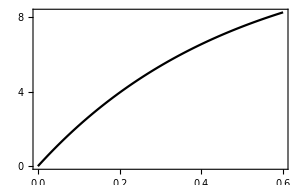

```mathematica
(* Remove assumption of unloaded beam *)
(* izero initial electron beam current *)
izero=Quantity[80*milli,"Amperes"];
(* Assume beam loaded, i.e. beam current is nonzero through structure *)
(* Assume no input power from the RF generator *)
(* Keep assumption of constant impedance structure *)
(* 5.21 The peak beam-induced field which opposes the motion of the beam. *)
(* alpha is indendent of z and is constant through structure *)
eb[z_,izero_]:=izero*r*(1-E^(-alpha*Quantity[z,"Meter"]));
Plot[eb[z,izero]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","E_b","MV/m"]]]
```

```mathematica
eb[0,izero]
```

0. A Ω/m

```mathematica
(* 5.22 The integrated induced electric field *)
Integrate[eb[z,izero],{z,0,QuantityMagnitude[L]}]
```

2.97675×10^6 V/m

```mathematica
(* Alternatively integrate 5.22 analytically *)
vb[izero_]:=izero*r*L*(1-(1-E^(-tau))/tau);
vb[izero]
```

2.97675×10^6 A Ω

```mathematica
(* 5.23 The "beam loading coefficient" *)
(* 5.23 The net voltage gain *)
vLoaded[r_,L_,tau_,pzero_,izero_]:=vzero[r,L,tau,pzero]-r*L*(1-(1-E^(-tau))/tau)*izero
vLoaded[r,L,tau,pzero,izero]
```

7.96117×10^6 A Ω

```mathematica
particleEnergyGainLoaded[r_,L_,tau_,pzero_,izero_]:=
```

```mathematica
(* Amps Ohms = Volt *)
functions={};
Do[AppendTo[functions,vLoaded[r,L,tau,pzero,Quantity[izeroo,"Amperes"]]/mega],{tau,tauList}]
(* net voltage gain of beam, beam loaded, constant impedance *)
vLoadedPlot=Plot[{functions,10},{izeroo,iZeroMin,iZeroMax},FrameLabel->{"Beam Current [A]","Voltage [MV]"},PlotStyle->plotstyledashed,PlotRange->{All,{0,21}},ImagePadding->55];
(* plotrange 60cm 16 *)
(* plotrange 80cm also 16 *)
```

```mathematica
(* average beam power of beam loaded structure, constant impedance *)
pAverage[r_,L_,tau_,pzero_,izero_,duty_]:=vLoaded[r,L,tau,pzero,Quantity[izero,"Amperes"]]*Quantity[izero,"Amperes"]*duty;
functions={};
Do[AppendTo[functions,pAverage[r,L,tau,pzero,izeroo,duty]],{tau,tauList}]
pAveragePlot=Plot[{functions,500},{izeroo,iZeroMin,iZeroMax},FrameLabel->{{None,"Beam Power [W]"},{None,None}},
FrameTicks->{{None,All},{None,None}},PlotRange->{All,{0,1050}},ImagePadding->55,PlotStyle->plotstyle];
```

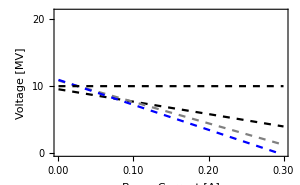
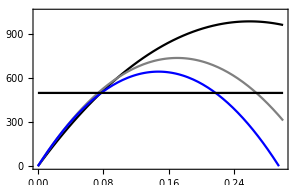

```mathematica
Overlay[{vLoadedPlot,pAveragePlot}]
```

```mathematica
(* Export["/Users/user1/Desktop/cz.pdf",%] *)
```

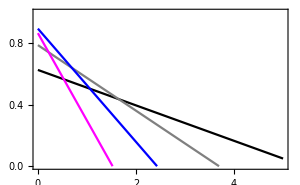

```mathematica
(* Normalize beam current and net voltage gain *)
(* Fig 5.2 The net voltage gain as function of beam current, as function of tau. *)
iZeroFromNormalized[iNormalized_]:=iNormalized*(r*L)^(-1/2)*pzero^(1/2)
vNormalized[r_,L_,tau_,pzero_,iNormalized_]:=vLoaded[r,L,tau,pzero,iZeroFromNormalized[iNormalized]]*(r*L*pzero)^(-1/2)
Plot[{vNormalized[r,L,0.25,pzero,iNormalized],
vNormalized[r,L,0.5,pzero,iNormalized],
vNormalized[r,L,1.0,pzero,iNormalized],
vNormalized[r,L,2.0,pzero,iNormalized]},{iNormalized,0,5},FrameLabel->{MaTeX["\\textrm{Normalized Beam Current }I_{0,N}"],MaTeX["\\textrm{Normalized Net Voltage Gain }V_N"]},PlotRange->{All,{0,1}},PlotStyle->{Black,Gray,Blue, Magenta}]
```

```mathematica
(* power transferred to the beam. its quadratic as function of beam current *)
pbeam=vLoaded[r,L,tau,pzero,izero]*izero
```

636893. A^2 Ω

```mathematica
(* amps^2 ohm = watt *)
(* efficiency *)
eta=pbeam/pzero
```

0.374643

```mathematica
0.30074869599608695
```

0.300749

```mathematica
(* 5.25 the maximum efficiency is when initial beam current is *)
vzero[r,L,tau,pzero]/(2*m[r,L,tau])
```

(5.46896×10^6 √Ω √W)/m[144000000 Ω/m,0.6 m,1.25643]

```mathematica
(* corresponding to the maximum efficiency *)
etamax=vzero[r,L,tau,pzero]^2*(4*m[r,L,tau]*pzero)^(-1)
```

(1.75938×10^7 Ω)/m[144000000 Ω/m,0.6 m,1.25643]

```mathematica
(* 5.26 energy at the end of the structure *)
eLLoaded=ezero[alpha,r,pzero]*E^(-tau)-izero*r(1-E^(-tau))
```

874306. A Ω/m

```mathematica
(* 5.26 power flowing into terminator, beam loaded, travelling wave *)
pLLoaded=eLLoaded^2*L*(2*tau*r)^(-1)
```

1267.5 A^2 Ω

```mathematica
(* power dissipated in the structure *)
pIntoStructure=pzero-pLLoaded-izero*vLoaded[r,L,tau,pzero,izero]
```

1.06184×10^6 A^2 Ω